```mathematica
ds=ResourceData["Patient Medical Data for Novel Coronavirus 2019-nCoV from Wuhan, China"]
```

```mathematica
ds[1;;3]
```

```mathematica
ds[1;;3,{"Age","Sex","City"}]
```

```mathematica
ds[Tally,"Sex"]
```

```mathematica
ds[Select[Not[MissingQ[#Age]]&],"Age"]
```

```mathematica
ds2=ds[Select[Not[MissingQ[#Age]]&&Head[#Age]=!=Interval&],N[#Age]&]
```

```mathematica
ds2[Mean]
```

46.3221

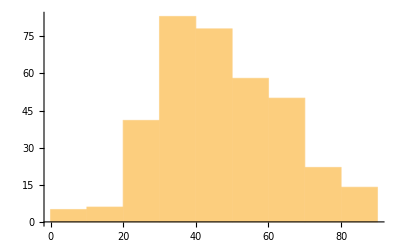

```mathematica
Histogram[Normal[ds2]]
```

```mathematica
ReverseSortBy[Tally[Flatten[Normal[ds[Select[Not[MissingQ[#ChronicDiseases]]&],"ChronicDiseases"]]]],Last]//Grid
```

hypertension | 15
diabetes | 11
coronary heart disease | 5
chronic bronchitis | 3
Parkinson's disease | 2
coronary stent | 2
cerebral infarction | 2
type 2 diabetes | 1
Tuberculosis | 1
stenocardia | 1
lung cancer | 1
hip replacement | 1
hemorrhage of digestive tract | 1
frequent ventricular premature beat | 1
encephalomalacia | 1
colon cancer | 1
chronic renal insufficiency | 1
chronic obstructive pulmonary disease | 1